```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,mathtools}"}];
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

```mathematica
$K = 3;
```

```mathematica
If[!DirectoryQ["../plots-3"], CreateDirectory["../plots-3"]];
```

```mathematica
Do[data[k] = {}, {k, 2, 1+$K($K+1)}];
Do[Module[{}, (
d = Import["../../runs/Stats-New-2/N"<>ToString@$N<>"K"<>ToString@$K<>".dat"];
Do[AppendTo[data[k], {$N, Around[d[[All, k]]]}], {k, 2, 3}];
Do[AppendTo[data[k], {$N, Around[d[[All, k]]/d[[All, 2]]]}], {k, 4, 1+$K($K+1), 2}];
Do[AppendTo[data[k], {$N, Around[d[[All, k]]/d[[All, 3]]]}], {k, 5, 1+$K($K+1), 2}];
)], {$N, 3, 9}]
```

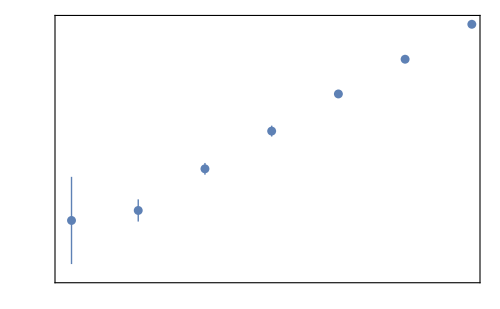

```mathematica
(* Mean of TrX^2 *)
plt1 = ListPlot[data[2],
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
FrameLabel->MaTeX/@{"N", "\\expval{\\Tr X^2}_t"},
FrameTicks->{{With[{ticks=2.5+0.5Range[0,6]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=Range[2,9]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
ImageSize->500
];
(*Export["../plots-3/monopole-mean.pdf", plt1, ImageResolution->300];*)
plt1
```

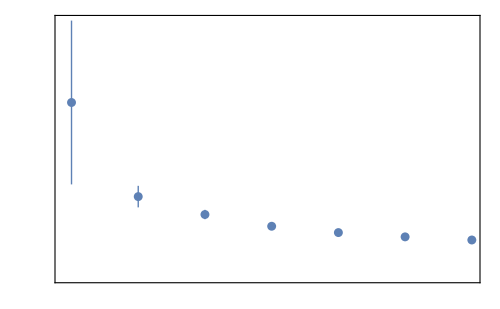

```mathematica
(* SD of TrX^2 *)
plt2 = ListPlot[data[3],
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotRange->All,
FrameLabel->MaTeX/@{"N", "\\sigma(\\Tr X^2)_t"},
FrameTicks->{{With[{ticks=0.0+0.5Range[0,6]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=Range[2,9]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
ImageSize->500
];
(*Export["../plots-3/monopole-sd.pdf", plt2, ImageResolution->300];*)
plt2
```

```mathematica
latexExp[i_, j_] := Module[{}, (
If[i == j, 
"\\frac{2}{3}\\Tr (X^{"<>ToString@i<>"})^2"<>StringJoin@Table[If[k==i, Nothing, " - \\frac{1}{3} \\Tr (X^{"<>ToString@k<>"})^2"], {k, 1, $K}],
"\\Tr X^{"<>ToString@i<>"} X^{"<>ToString@j<>"}"
]
)];
```

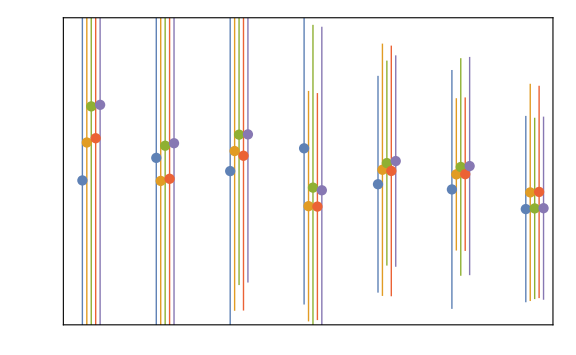

```mathematica
(* Mean of SymTr *)
plt3 = ListPlot[Table[Table[{data[k][[A, 1]]+0.03(k-3-$K($K+1)/2), data[k][[A, 2]]}, {A, 1, Length[data[k]]}], {k, 4, 1+$K($K+1), 2}],
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
FrameLabel->MaTeX/@{"N", "\\expval{\\Tr X^i X^j - \\frac{\\delta^{i j}}{K} \\Tr X^2}_t"},
FrameTicks->{{With[{ticks=-0.4+0.2Range[0,6]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=Range[2,9]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
PlotLegends->MaTeX/@(Flatten@Table[latexExp[i, j], {i, 1, $K-1}, {j, i, $K}]),
ImageSize->Large
];
(*Export["../plots-3/quadrupole-mean.pdf", Rasterize[plt3, ImageResolution->300]];*)
plt3
```

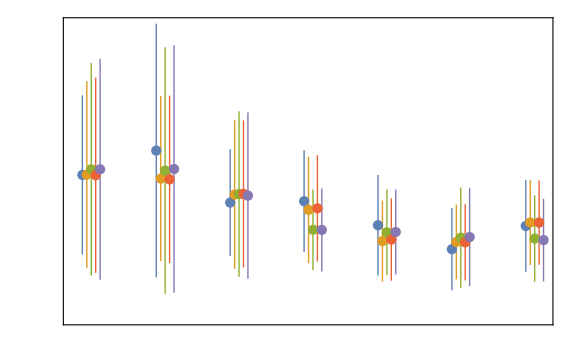

```mathematica
(* SD of SymTr *)
plt4 = ListPlot[Table[Table[{data[k][[A, 1]]+0.03(k-3-$K($K+1)/2), data[k][[A, 2]]}, {A, 1, Length[data[k]]}], {k, 5, 1+$K($K+1), 2}],
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
FrameLabel->MaTeX/@{"N", "\\sigma(\\Tr X^i X^j - \\frac{\\delta^{i j}}{K} \\Tr X^2)_t"},
FrameTicks->{{With[{ticks=0+0.2Range[0,6]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=Range[2,9]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
PlotLegends->MaTeX/@(Flatten@Table[latexExp[i, j], {i, 1, $K-1}, {j, i, $K}]),
ImageSize->Large
];
(*Export["../plots-3/quadrupole-sd.pdf", Rasterize[plt4, ImageResolution->300, ImageSize->Large]];*)
plt4
```